### Band Structure from PROCAR_OPT @Henry Pinto, YTU

The following notebook will allow you to create the band structure from any VASP calculation that produces a PROCAR_OPT file

To run this notebook, be sure you have  in same directory  PROCAR_OPT and KPOINTS_OPT.

%%%% you can run the lines below %%%%%%%%%

```mathematica
SetDirectory["/home/rolando/Downloads/Yachay/8th_Semester/dft/dft_coursework/midterm/test/results"]
```

/home/rolando/Downloads/Yachay/8th_Semester/dft/dft_coursework/midterm/test/results

```mathematica
Run["grep k-point PROCAR_OPT > kpt"];
Run["sed 's/-/ -/g' kpt > kpt2"];
Run["sed 's/k -point/k-point/g' kpt2 > kpts"];
Run["rm kpt kpt2"];
Run["grep band PROCAR_OPT > bandData"];
Run["grep \"# of bands\" PROCAR_OPT | tail -1 > numbands"];
```

```mathematica
input=Import["DOSCAR-bulk", "Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

9.0314

```mathematica
(*This gets number of kp and bands*)
bandsinfo=Import["numbands","Table"][[1]];
{Nkpt,Nbands}=bandsinfo//{#[[4]],#[[8]]}&
```

{140,8}

```mathematica
(*This gets the high symmetry points and divisions*)
path=Import["KPOINTS-bs","Table"];
div=path[[2,1]];
```

```mathematica
(*This defines the high symmetry points labels and the length*)
hsympts=(If[(path[[5]]//Length)==4,path[[5;;-1]]//Flatten//Partition[#,4]&//#[[All,4]]&, path[[5;;-1]]//Flatten//Partition[#,5]&//#[[All,5]]&]//Drop[#,{3,Length[#],2}]&)/."GAMMA"->"Γ"
NumGridL=(hsympts//Length)-2;
```

{Γ,Y,M,A,Γ}

```mathematica
(*This defines the band energies shifted to Ef*)
bands=Import["bandData","Table"][[2;;Nbands Nkpt+1]][[All,5]]-ef//Partition[#,Nbands]&;
bandener=bands//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This defines k-point coordinates*)
kp=Import["kpts","Table"][[2;;Nkpt+1]][[All,{4,5,6}]];
kpt=kp//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This liniarizes k-point coordinates in 1D*)
kpt2=Join[{0},Table[Norm[kpt[[i+1]]-kpt[[i]]],{i,(kpt//Length)-1}]]//Accumulate;
```

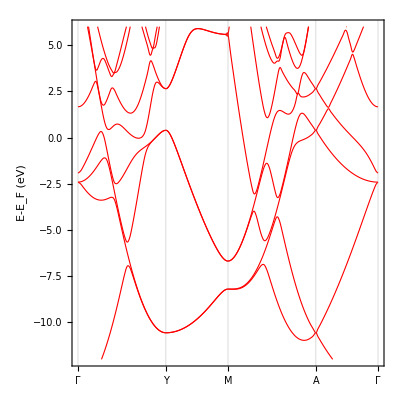

```mathematica
(*This creates the bands in kpt2 domain*)
bands2={kpt2,bandener}//Transpose;
Do[bd[i]=bands2//Map[{#[[1]],#[[2,i]]}&,#]&,{i,Nbands}];

(*please provide the bands you want to plot*)
ListPlot[Table[bd[i],{i,1,8(*Nbands*)}],
Frame->True,
FrameLabel->{"","E-E_F (eV)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->14},
Joined->True,
InterpolationOrder->2,
AspectRatio->1,
AxesStyle->Directive[Black,Dashed, AbsoluteThickness[0.7]],
FrameTicks->{{Automatic,None},{{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],hsympts}//Transpose,None}},
GridLines->{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],None},
PlotStyle->Directive[Red,AbsoluteThickness[0.8]],
PlotRange->{{0,kpt2[[-1]]},{-12,6}}]
```